## Forcing the frequencies

```mathematica
eq1:=X[r]+2G[r]-2A[r]==Subscript[γ, b];
eq2:=X'[r]-2A'[r]-2G[r]A[r]+2G[r]X[r]-2 G[r]^2==X'[r]-2G'[r]+G[r]X[r]-G[r]A[r]-2 G[r]^2-A[r]^2+A[r]X[r];
eq3:=A[r]+X[r]-G[r]==Subscript[γ, f];
FullSimplify[eq1]
FullSimplify[eq2]
FullSimplify[eq3]
```

2 A[r]+γ_b==2 G[r]+X[r]

(A[r]-G[r]) (A[r]-X[r])+2 G'[r]==2 A'[r]

A[r]+X[r]==G[r]+γ_f

```mathematica
Solve[eq1,X[r]]
```

{{X[r]→2 A[r]-2 G[r]+γ_b}}

```mathematica
X[r_]:=2 A[r]-2 G[r]+Subscript[γ, b];
FullSimplify[eq1]
FullSimplify[eq2]
FullSimplify[eq3]
```

True

(A[r]-G[r]) (A[r]-2 G[r]+γ_b)+2 (A'[r]-G'[r])==0

3 A[r]+γ_b==3 G[r]+γ_f

```mathematica
Solve[eq3,A[r]]
```

{{A[r]→1/3 (3 G[r]-γ_b+γ_f)}}

```mathematica
A[r_]:=1/3 (3 G[r]-Subscript[γ, b]+Subscript[γ, f]);
FullSimplify[eq1]
FullSimplify[eq2]
FullSimplify[eq3]
```

True

(3 G[r]-2 γ_b-γ_f) (γ_b-γ_f)==0

True

```mathematica
FullSimplify[DSolve[eq2,G[r],r]]
```

{{G[r]→1/3 (2 γ_b+γ_f)}}

```mathematica
G[r_]:=1/3 (2 Subscript[γ, b]+Subscript[γ, f]);
FullSimplify[eq1]
FullSimplify[eq2]
FullSimplify[eq3]
```

True

True

True

```mathematica
FullSimplify[A[r]]
FullSimplify[G[r]]
FullSimplify[X[r]]
```

1/3 (γ_b+2 γ_f)

1/3 (2 γ_b+γ_f)

1/3 (γ_b+2 γ_f)

```mathematica
HC1:=B''[r]+B'[r]*(X[r]+2*G[r]-2*A[r])+2*B[r]*(G[r]*(X[r]-A[r]-G[r])-A'[r]+X'[r]/2);
HC2:=F''[r]+F'[r]*(A[r]+X[r]-G[r])+F[r]*(X'[r]-2*G[r]^2+(A[r]+G[r])*(X[r]-A[r]))-G[r];
Expand[HC1==0]
Expand[DSolve[HC1==0,B[r],r]]
Expand[HC2==0]
Expand[DSolve[HC2==0,F[r],r]]
```

-8/9 B[r] γ_b^2-8/9 B[r] γ_b γ_f-2/9 B[r] γ_f^2+γ_b B'[r]+B''[r]==0

{{B[r]→ⅇ^(1/6 r (-3 γ_b-√(41 γ_b^2+32 γ_b γ_f+8 γ_f^2))) C[1]+ⅇ^(1/6 r (-3 γ_b+√(41 γ_b^2+32 γ_b γ_f+8 γ_f^2))) C[2]}}

-(2 γ_b)/3-8/9 F[r] γ_b^2-γ_f/3-8/9 F[r] γ_b γ_f-2/9 F[r] γ_f^2+γ_f F'[r]+F''[r]==0

{{F[r]→ⅇ^(1/6 r (-3 γ_f-√(32 γ_b^2+32 γ_b γ_f+17 γ_f^2))) C[1]+ⅇ^(1/6 r (-3 γ_f+√(32 γ_b^2+32 γ_b γ_f+17 γ_f^2))) C[2]-(3 γ_b)/(4 γ_b^2+4 γ_b γ_f+γ_f^2)-(3 γ_f)/(2 (4 γ_b^2+4 γ_b γ_f+γ_f^2))}}

```mathematica
B[r_]:=ⅇ^(1/6 r (-3 Subscript[γ, b]-√(41 Subscript[γ, b]^2+32 Subscript[γ, b] Subscript[γ, f]+8 Subscript[γ, f]^2))) Subscript[B, 1]+ⅇ^(1/6 r (-3 Subscript[γ, b]+√(41 Subscript[γ, b]^2+32 Subscript[γ, b] Subscript[γ, f]+8 Subscript[γ, f]^2))) Subscript[B, 2];
F[r_]:=ⅇ^(1/6 r (-3 Subscript[γ, f]-√(32 Subscript[γ, b]^2+32 Subscript[γ, b] Subscript[γ, f]+17 Subscript[γ, f]^2))) Subscript[F, 1]+ⅇ^(1/6 r (-3 Subscript[γ, f]+√(32 Subscript[γ, b]^2+32 Subscript[γ, b] Subscript[γ, f]+17 Subscript[γ, f]^2))) Subscript[F, 2]-(3 Subscript[γ, b])/(4 Subscript[γ, b]^2+4 Subscript[γ, b] Subscript[γ, f]+Subscript[γ, f]^2)-(3 Subscript[γ, f])/(2 (4 Subscript[γ, b]^2+4 Subscript[γ, b] Subscript[γ, f]+Subscript[γ, f]^2));
```

```mathematica
Rtt[r_]:=B'[r]+B[r]*(2*G[r]+X[r]-A[r]);
Rrr[r_]:=A'[r]+2G'[r]+A[r]A[r]+2G[r]G[r]-A[r]X[r]-2X[r]G[r];
Rthth[r_]:=F'[r]+F[r](A[r]+X[r])+1;
FullSimplify[Rtt[r]]
FullSimplify[Rrr[r]]
FullSimplify[Rthth[r]]
```

1/6 ⅇ^(-1/6 r (3 γ_b+√(41 γ_b^2+32 γ_b γ_f+8 γ_f^2))) (B_1 (5 γ_b+4 γ_f-√(41 γ_b^2+32 γ_b γ_f+8 γ_f^2))+ⅇ^(1/3 r √(41 γ_b^2+32 γ_b γ_f+8 γ_f^2)) B_2 (5 γ_b+4 γ_f+√(41 γ_b^2+32 γ_b γ_f+8 γ_f^2)))

2/9 (γ_b-γ_f) (2 γ_b+γ_f)

1/6 (-6+(18 γ_b)/(2 γ_b+γ_f)+ⅇ^(-1/6 r (3 γ_f+√(32 γ_b^2+32 γ_b γ_f+17 γ_f^2))) F_1 (4 γ_b+5 γ_f-√(32 γ_b^2+32 γ_b γ_f+17 γ_f^2))+ⅇ^(1/6 r (-3 γ_f+√(32 γ_b^2+32 γ_b γ_f+17 γ_f^2))) F_2 (4 γ_b+5 γ_f+√(32 γ_b^2+32 γ_b γ_f+17 γ_f^2)))

```mathematica
FullSimplify[Rtt[0]]
FullSimplify[Rrr[0]]
FullSimplify[Rthth[0]]
```

1/6 (B_1 (5 γ_b+4 γ_f-√(41 γ_b^2+32 γ_b γ_f+8 γ_f^2))+B_2 (5 γ_b+4 γ_f+√(41 γ_b^2+32 γ_b γ_f+8 γ_f^2)))

2/9 (γ_b-γ_f) (2 γ_b+γ_f)

1/6 (3-(9 γ_f)/(2 γ_b+γ_f)+F_1 (4 γ_b+5 γ_f-√(32 γ_b^2+32 γ_b γ_f+17 γ_f^2))+F_2 (4 γ_b+5 γ_f+√(32 γ_b^2+32 γ_b γ_f+17 γ_f^2)))

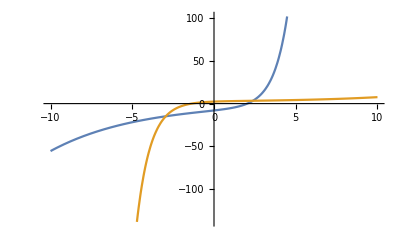

```mathematica
Subscript[F, 1]=1;Subscript[F, 2]=1;Subscript[B, 1]=10;Subscript[B, 2]=1;Subscript[γ, b]=-1;Subscript[γ, f]=1;
Plot[{Rtt[r],Rthth[r]},{r,-10,10}]
```

## Auto-parallel curves

```mathematica
eq1t[τ_]:=t''[τ]+2*A[r[τ]]*r'[τ]*t'[τ];
FullSimplify[eq1t[τ]]
eq1r[τ_]=r''[τ]+B[r[τ]]*t'[τ]^2+X[r[τ]]*r'[τ]^2+F[r[τ]]*θ'[τ]^2+F[r[τ]]*ϕ'[τ]^2*Sin[θ]^2;
FullSimplify[eq1r[τ]]
eq1th[τ_]=θ''[τ]+2*G[r[τ]]*θ'[τ]*r'[τ]-Cos[θ]*Sin[θ]*ϕ'[τ]^2;
FullSimplify[eq1th[τ]]
eq1ph[τ_]=ϕ''[τ]+2*G[r[τ]]*ϕ'[τ]*r'[τ]+Cos[θ]/Sin[θ]*ϕ'[τ]*θ'[τ];
FullSimplify[eq1ph[τ]]
```

2/3 (γ_b+2 γ_f) r'[τ] t'[τ]+t''[τ]

1/3 (γ_b+2 γ_f) r'[τ]^2+ⅇ^(-1/6 r[τ] (3 γ_b+√(41 γ_b^2+32 γ_b γ_f+8 γ_f^2))) B_1 t'[τ]^2+ⅇ^(1/6 r[τ] (-3 γ_b+√(41 γ_b^2+32 γ_b γ_f+8 γ_f^2))) B_2 t'[τ]^2+1/2 (2 ⅇ^(-1/6 r[τ] (3 γ_f+√(32 γ_b^2+32 γ_b γ_f+17 γ_f^2))) (F_1+ⅇ^(1/3 r[τ] √(32 γ_b^2+32 γ_b γ_f+17 γ_f^2)) F_2)-3/(2 γ_b+γ_f)) (θ'[τ]^2+Sin[θ]^2 ϕ'[τ]^2)+r''[τ]

2/3 (2 γ_b+γ_f) r'[τ] θ'[τ]-Cos[θ] Sin[θ] ϕ'[τ]^2+θ''[τ]

2/3 (2 γ_b+γ_f) r'[τ] ϕ'[τ]+Cot[θ] θ'[τ] ϕ'[τ]+ϕ''[τ]

Fixing θ=π/2

```mathematica
eq1t[τ_]:=t''[τ]+2*A[r[τ]]*r'[τ]*t'[τ];
FullSimplify[eq1t[τ]]
eq1r[τ_]=r''[τ]+B[r[τ]]*t'[τ]^2+X[r[τ]]*r'[τ]^2+F[r[τ]]*ϕ'[τ]^2;
FullSimplify[eq1r[τ]]
eq1ph[τ_]=ϕ''[τ]+2*G[r[τ]]*ϕ'[τ]*r'[τ];
FullSimplify[eq1ph[τ]]
```

2/3 (γ_b+2 γ_f) r'[τ] t'[τ]+t''[τ]

1/3 (γ_b+2 γ_f) r'[τ]^2+ⅇ^(-1/6 r[τ] (3 γ_b+√(41 γ_b^2+32 γ_b γ_f+8 γ_f^2))) (B_1+ⅇ^(1/3 r[τ] √(41 γ_b^2+32 γ_b γ_f+8 γ_f^2)) B_2) t'[τ]^2+1/2 (2 ⅇ^(-1/6 r[τ] (3 γ_f+√(32 γ_b^2+32 γ_b γ_f+17 γ_f^2))) (F_1+ⅇ^(1/3 r[τ] √(32 γ_b^2+32 γ_b γ_f+17 γ_f^2)) F_2)-3/(2 γ_b+γ_f)) ϕ'[τ]^2+r''[τ]

2/3 (2 γ_b+γ_f) r'[τ] ϕ'[τ]+ϕ''[τ]

```mathematica
DSolve[2/3 (2 Subscript[γ, b]+Subscript[γ, f]) r'[τ] ϕ'[τ]+ϕ''[τ]==0,ϕ[τ],τ]
```

{{ϕ[τ]→C[2]+ⅇ^(-4/3 r[K[1]] γ_b-2/3 r[K[1]] γ_f) C[1]K[1]1τ}}

```mathematica
D[ⅇ^(-4/3 r[K[1]] Subscript[γ, b]-2/3 r[K[1]] Subscript[γ, f]) Subscript[ϕ, 0]K[1]1τ,τ]
```

ⅇ^(-4/3 r[τ] γ_b-2/3 r[τ] γ_f) ϕ_0

```mathematica
ϕ[τ_]:=ⅇ^(-4/3 r[K[1]] Subscript[γ, b]-2/3 r[K[1]] Subscript[γ, f]) *(Subscript[ϕ, 0])K[1]1τ;
eq1t[τ_]:=t''[τ]+2*A[r[τ]]*r'[τ]*t'[τ];
FullSimplify[eq1t[τ]]
eq1r[τ_]=r''[τ]+B[r[τ]]*t'[τ]^2+X[r[τ]]*r'[τ]^2+F[r[τ]]*ϕ'[τ]^2;
FullSimplify[eq1r[τ]]
eq1ph[τ_]=ϕ''[τ]+2*G[r[τ]]*ϕ'[τ]*r'[τ];
FullSimplify[eq1ph[τ]]
```

2/3 (γ_b+2 γ_f) r'[τ] t'[τ]+t''[τ]

(ⅇ^(-4/3 r[τ] (2 γ_b+γ_f)) (-3+2 ⅇ^(-1/6 r[τ] (3 γ_f+√(32 γ_b^2+32 γ_b γ_f+17 γ_f^2))) (F_1+ⅇ^(1/3 r[τ] √(32 γ_b^2+32 γ_b γ_f+17 γ_f^2)) F_2) (2 γ_b+γ_f)) ϕ_0^2)/(2 (2 γ_b+γ_f))+1/3 (γ_b+2 γ_f) r'[τ]^2+ⅇ^(-1/6 r[τ] (3 γ_b+√(41 γ_b^2+32 γ_b γ_f+8 γ_f^2))) (B_1+ⅇ^(1/3 r[τ] √(41 γ_b^2+32 γ_b γ_f+8 γ_f^2)) B_2) t'[τ]^2+r''[τ]

0

```mathematica
DSolve[2/3 (Subscript[γ, b]+2 Subscript[γ, f]) r'[τ] t'[τ]+t''[τ]==0,t[τ],τ]
```

{{t[τ]→C[2]+ⅇ^(-2/3 r[K[1]] γ_b-4/3 r[K[1]] γ_f) C[1]K[1]1τ}}

```mathematica
D[ⅇ^(-2/3 r[K[1]] Subscript[γ, b]-4/3 r[K[1]] Subscript[γ, f]) Subscript[t, 0]K[1]1τ,τ]
```

ⅇ^(-2/3 r[τ] γ_b-4/3 r[τ] γ_f) t_0

```mathematica
t[τ_]:=ⅇ^(-2/3 r[K[1]] Subscript[γ, b]-4/3 r[K[1]] Subscript[γ, f]) Subscript[t, 0]K[1]1τ;
eq1t[τ_]:=t''[τ]+2*A[r[τ]]*r'[τ]*t'[τ];
FullSimplify[eq1t[τ]]
eq1r[τ_]=r''[τ]+B[r[τ]]*t'[τ]^2+X[r[τ]]*r'[τ]^2+F[r[τ]]*ϕ'[τ]^2;
FullSimplify[eq1r[τ]]
eq1ph[τ_]=ϕ''[τ]+2*G[r[τ]]*ϕ'[τ]*r'[τ];
FullSimplify[eq1ph[τ]]
```

0

ⅇ^(-1/6 r[τ] (11 γ_b+16 γ_f+√(41 γ_b^2+32 γ_b γ_f+8 γ_f^2))) (B_1+ⅇ^(1/3 r[τ] √(41 γ_b^2+32 γ_b γ_f+8 γ_f^2)) B_2) t_0^2+(ⅇ^(-4/3 r[τ] (2 γ_b+γ_f)) (-3+2 ⅇ^(-1/6 r[τ] (3 γ_f+√(32 γ_b^2+32 γ_b γ_f+17 γ_f^2))) (F_1+ⅇ^(1/3 r[τ] √(32 γ_b^2+32 γ_b γ_f+17 γ_f^2)) F_2) (2 γ_b+γ_f)) ϕ_0^2)/(2 (2 γ_b+γ_f))+1/3 (γ_b+2 γ_f) r'[τ]^2+r''[τ]

0

A numerical solution to the above differential equation

3/2 ⅇ^((4 r[τ])/3)+2 ⅇ^((37 r[τ])/6) Cosh[1/6 √17 r[τ]]+2 ⅇ^((17 r[τ])/6) Cosh[1/6 √89 r[τ]]-5/3 r'[τ]^2+r''[τ]

{{r[τ]→InterpolatingFunction[…][τ]}}

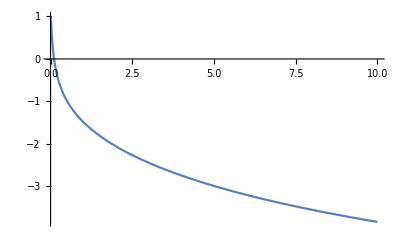

```mathematica
Subscript[γ, b]=1;Subscript[γ, f]=-3;
eq1r[τ_]=r''[τ]+B[r[τ]]*t'[τ]^2+X[r[τ]]*r'[τ]^2+F[r[τ]]*ϕ'[τ]^2;
FullSimplify[eq1r[τ]/.{Subscript[B, 1]->1,Subscript[B, 2]->1,Subscript[F, 1]->1,Subscript[F, 2]->1,Subscript[t, 0]->1,Subscript[ϕ, 0]->1}]
s=NDSolve[{%==0,r[0]==1,r'[0]==0},r[τ],{τ,0,10}]
Plot[r[τ]/.s,{τ,0,10}]
```

```mathematica
FullSimplify[Rtt[r]]
FullSimplify[Rrr[r]]
FullSimplify[Rthth[r]]
```

1/6 ⅇ^(-1/6 (3+√17) r) (-((7+√17) B_1)+(-7+√17) ⅇ^((√17 r)/3) B_2)

-8/9

1/6 (-24-(11+√89) ⅇ^(-1/6 (-9+√89) r) F_1+(-11+√89) ⅇ^(1/6 (9+√89) r) F_2)

In the limit for r to infinity

```mathematica
Limit[Rtt[r],r->∞]
FullSimplify[Limit[Rrr[r],r->∞]]
Limit[Rthth[r],r->∞]
```

C[2] (-∞)

-8/9

C[4] (-∞)

De Sitter metric

```mathematica
gtt[r_]:=-(1-(2*a)/r-b*r^2);
grr[r_]:=1/(1-(2*a)/r-b*r^2) ;
gthth[r_]:=r^2;
Limit[gtt[r],r->∞]
FullSimplify[Limit[grr[r],r->∞]]
Limit[gthth[r],r->∞]
```

b ∞

0

∞

Anti de Sitter

```mathematica
gtt[r_]:=-(1-a/r+b*r^2);
grr[r_]:=1/(1-a/r+b*r^2) ;
gthth[r_]:=r^2;
gthth[r_]:=r^2;
Limit[gtt[r],r->∞]
FullSimplify[Limit[grr[r],r->∞]]
Limit[gthth[r],r->∞]
```

b (-∞)

0

∞

## From another view point, light rays

```mathematica
FullSimplify[Rtt[r]]
FullSimplify[Rrr[r]]
FullSimplify[Rthth[r]]
FullSimplify[Rthth[r]*(sin[θ])^2]
```

1/6 ⅇ^(-1/6 r (3 γ_b+√(41 γ_b^2+32 γ_b γ_f+8 γ_f^2))) (B_1 (5 γ_b+4 γ_f-√(41 γ_b^2+32 γ_b γ_f+8 γ_f^2))+ⅇ^(1/3 r √(41 γ_b^2+32 γ_b γ_f+8 γ_f^2)) B_2 (5 γ_b+4 γ_f+√(41 γ_b^2+32 γ_b γ_f+8 γ_f^2)))

2/9 (γ_b-γ_f) (2 γ_b+γ_f)

1/6 (-6+(18 γ_b)/(2 γ_b+γ_f)+ⅇ^(-1/6 r (3 γ_f+√(32 γ_b^2+32 γ_b γ_f+17 γ_f^2))) F_1 (4 γ_b+5 γ_f-√(32 γ_b^2+32 γ_b γ_f+17 γ_f^2))+ⅇ^(1/6 r (-3 γ_f+√(32 γ_b^2+32 γ_b γ_f+17 γ_f^2))) F_2 (4 γ_b+5 γ_f+√(32 γ_b^2+32 γ_b γ_f+17 γ_f^2)))

1/6 sin[θ]^2 (-6+(18 γ_b)/(2 γ_b+γ_f)+ⅇ^(-1/6 r (3 γ_f+√(32 γ_b^2+32 γ_b γ_f+17 γ_f^2))) F_1 (4 γ_b+5 γ_f-√(32 γ_b^2+32 γ_b γ_f+17 γ_f^2))+ⅇ^(1/6 r (-3 γ_f+√(32 γ_b^2+32 γ_b γ_f+17 γ_f^2))) F_2 (4 γ_b+5 γ_f+√(32 γ_b^2+32 γ_b γ_f+17 γ_f^2)))

Caso ‘momento angular’ = 0 y ‘energia = 0’

```mathematica
LE:=Rrr[r[τ]]*(r'[τ])^2==0;
Simplify[LE]
```

(2 γ_b^2-γ_b γ_f-γ_f^2) r'[τ]==0

```mathematica
DSolve[LE,r[τ],τ]
```

{{r[τ]→C[1]}}

```mathematica
LE:=Rtt[r[τ]]*(ⅇ^(-2/3 r[τ] Subscript[γ, b]-4/3 r[τ] Subscript[γ, f]) Subscript[t, 0])^2+Rrr[r[τ]]*(r'[τ])^2==0;
Simplify[LE]
```

3 ⅇ^(1/6 r[τ] (-11 γ_b-16 γ_f+√(41 γ_b^2+32 γ_b γ_f+8 γ_f^2))) B_2 t_0^2 (5 γ_b+4 γ_f+√(41 γ_b^2+32 γ_b γ_f+8 γ_f^2))+4 (2 γ_b^2-γ_b γ_f-γ_f^2) r'[τ]^2==3 ⅇ^(-1/6 r[τ] (11 γ_b+16 γ_f+√(41 γ_b^2+32 γ_b γ_f+8 γ_f^2))) B_1 t_0^2 (-5 γ_b-4 γ_f+√(41 γ_b^2+32 γ_b γ_f+8 γ_f^2))

Caso ‘energia = 0’

```mathematica
LE:=Rrr[r[τ]]*(r'[τ])^2+Rthth[r[τ]]*(ⅇ^(-4/3 r[τ] Subscript[γ, b]-2/3 r[τ] Subscript[γ, f]) Subscript[ϕ, 0])^2==0;
Simplify[LE]
```

1/6 ⅇ^(-4/3 r[τ] (2 γ_b+γ_f)) (6+(2 (γ_b+2 γ_f) (-3+2 ⅇ^(-1/6 r[τ] (3 γ_f+√(32 γ_b^2+32 γ_b γ_f+17 γ_f^2))) F_1 (2 γ_b+γ_f)+2 ⅇ^(1/6 r[τ] (-3 γ_f+√(32 γ_b^2+32 γ_b γ_f+17 γ_f^2))) F_2 (2 γ_b+γ_f)))/(2 γ_b+γ_f)+ⅇ^(1/6 r[τ] (-3 γ_f+√(32 γ_b^2+32 γ_b γ_f+17 γ_f^2))) F_2 (-3 γ_f+√(32 γ_b^2+32 γ_b γ_f+17 γ_f^2))-ⅇ^(-1/6 r[τ] (3 γ_f+√(32 γ_b^2+32 γ_b γ_f+17 γ_f^2))) F_1 (3 γ_f+√(32 γ_b^2+32 γ_b γ_f+17 γ_f^2))) ϕ_0^2+2/9 (2 γ_b^2-γ_b γ_f-γ_f^2) r'[τ]^2==0

```mathematica
FullSimplify[Solve[LE,r'[τ]]]
```

{{r'[τ]→-1/(2 √((γ_b-γ_f) (2 γ_b+γ_f)))√3 √(1/(2 γ_b+γ_f)ⅇ^(-1/6 r[τ] (16 γ_b+11 γ_f+√(32 γ_b^2+32 γ_b γ_f+17 γ_f^2))) (6 ⅇ^(1/6 r[τ] (3 γ_f+√(32 γ_b^2+32 γ_b γ_f+17 γ_f^2))) (-γ_b+γ_f)-(F_1+ⅇ^(1/3 r[τ] √(32 γ_b^2+32 γ_b γ_f+17 γ_f^2)) F_2) (2 γ_b+γ_f) (4 γ_b+5 γ_f)+2 F_1 γ_b √(32 γ_b^2+32 γ_b γ_f+17 γ_f^2)-2 ⅇ^(1/3 r[τ] √(32 γ_b^2+32 γ_b γ_f+17 γ_f^2)) F_2 γ_b √(32 γ_b^2+32 γ_b γ_f+17 γ_f^2)+F_1 γ_f √(32 γ_b^2+32 γ_b γ_f+17 γ_f^2)-ⅇ^(1/3 r[τ] √(32 γ_b^2+32 γ_b γ_f+17 γ_f^2)) F_2 γ_f √(32 γ_b^2+32 γ_b γ_f+17 γ_f^2)) ϕ_0^2)},{r'[τ]→1/(2 √((γ_b-γ_f) (2 γ_b+γ_f)))√3 √(1/(2 γ_b+γ_f)ⅇ^(-1/6 r[τ] (16 γ_b+11 γ_f+√(32 γ_b^2+32 γ_b γ_f+17 γ_f^2))) (6 ⅇ^(1/6 r[τ] (3 γ_f+√(32 γ_b^2+32 γ_b γ_f+17 γ_f^2))) (-γ_b+γ_f)-(F_1+ⅇ^(1/3 r[τ] √(32 γ_b^2+32 γ_b γ_f+17 γ_f^2)) F_2) (2 γ_b+γ_f) (4 γ_b+5 γ_f)+2 F_1 γ_b √(32 γ_b^2+32 γ_b γ_f+17 γ_f^2)-2 ⅇ^(1/3 r[τ] √(32 γ_b^2+32 γ_b γ_f+17 γ_f^2)) F_2 γ_b √(32 γ_b^2+32 γ_b γ_f+17 γ_f^2)+F_1 γ_f √(32 γ_b^2+32 γ_b γ_f+17 γ_f^2)-ⅇ^(1/3 r[τ] √(32 γ_b^2+32 γ_b γ_f+17 γ_f^2)) F_2 γ_f √(32 γ_b^2+32 γ_b γ_f+17 γ_f^2)) ϕ_0^2)}}

Caso mas general

```mathematica
LE:=Rtt[r[τ]]*(ⅇ^(-2/3 r[τ] Subscript[γ, b]-4/3 r[τ] Subscript[γ, f]) Subscript[t, 0])^2+Rrr[r[τ]]*(r'[τ])^2+Rthth[r[τ]]*(ⅇ^(-4/3 r[τ] Subscript[γ, b]-2/3 r[τ] Subscript[γ, f]) Subscript[ϕ, 0])^2==0;
Simplify[LE]
```

1/18 (-3 ⅇ^(-1/6 r[τ] (11 γ_b+16 γ_f+√(41 γ_b^2+32 γ_b γ_f+8 γ_f^2))) t_0^2 (B_1 (-5 γ_b-4 γ_f+√(41 γ_b^2+32 γ_b γ_f+8 γ_f^2))-ⅇ^(1/3 r[τ] √(41 γ_b^2+32 γ_b γ_f+8 γ_f^2)) B_2 (5 γ_b+4 γ_f+√(41 γ_b^2+32 γ_b γ_f+8 γ_f^2)))+3 ⅇ^(-4/3 r[τ] (2 γ_b+γ_f)) (6+(2 (γ_b+2 γ_f) (-3+2 ⅇ^(-1/6 r[τ] (3 γ_f+√(32 γ_b^2+32 γ_b γ_f+17 γ_f^2))) F_1 (2 γ_b+γ_f)+2 ⅇ^(1/6 r[τ] (-3 γ_f+√(32 γ_b^2+32 γ_b γ_f+17 γ_f^2))) F_2 (2 γ_b+γ_f)))/(2 γ_b+γ_f)+ⅇ^(1/6 r[τ] (-3 γ_f+√(32 γ_b^2+32 γ_b γ_f+17 γ_f^2))) F_2 (-3 γ_f+√(32 γ_b^2+32 γ_b γ_f+17 γ_f^2))-ⅇ^(-1/6 r[τ] (3 γ_f+√(32 γ_b^2+32 γ_b γ_f+17 γ_f^2))) F_1 (3 γ_f+√(32 γ_b^2+32 γ_b γ_f+17 γ_f^2))) ϕ_0^2+4 (2 γ_b^2-γ_b γ_f-γ_f^2) r'[τ]^2)==0

## Shape of the orbit

```mathematica
r'[τ]==(-1/(2 √((Subscript[γ, b]-Subscript[γ, f]) (2 Subscript[γ, b]+Subscript[γ, f])))√3 √(1/(2 Subscript[γ, b]+Subscript[γ, f])ⅇ^(-1/6 r[τ] (16 Subscript[γ, b]+11 Subscript[γ, f]+√(32 Subscript[γ, b]^2+32 Subscript[γ, b] Subscript[γ, f]+17 Subscript[γ, f]^2))) (6 ⅇ^(1/6 r[τ] (3 Subscript[γ, f]+√(32 Subscript[γ, b]^2+32 Subscript[γ, b] Subscript[γ, f]+17 Subscript[γ, f]^2))) (-Subscript[γ, b]+Subscript[γ, f])-(Subscript[F, 1]+ⅇ^(1/3 r[τ] √(32 Subscript[γ, b]^2+32 Subscript[γ, b] Subscript[γ, f]+17 Subscript[γ, f]^2)) Subscript[F, 2]) (2 Subscript[γ, b]+Subscript[γ, f]) (4 Subscript[γ, b]+5 Subscript[γ, f])+2 Subscript[F, 1] Subscript[γ, b] √(32 Subscript[γ, b]^2+32 Subscript[γ, b] Subscript[γ, f]+17 Subscript[γ, f]^2)-2 ⅇ^(1/3 r[τ] √(32 Subscript[γ, b]^2+32 Subscript[γ, b] Subscript[γ, f]+17 Subscript[γ, f]^2)) Subscript[F, 2] Subscript[γ, b] √(32 Subscript[γ, b]^2+32 Subscript[γ, b] Subscript[γ, f]+17 Subscript[γ, f]^2)+Subscript[F, 1] Subscript[γ, f] √(32 Subscript[γ, b]^2+32 Subscript[γ, b] Subscript[γ, f]+17 Subscript[γ, f]^2)-ⅇ^(1/3 r[τ] √(32 Subscript[γ, b]^2+32 Subscript[γ, b] Subscript[γ, f]+17 Subscript[γ, f]^2)) Subscript[F, 2] Subscript[γ, f] √(32 Subscript[γ, b]^2+32 Subscript[γ, b] Subscript[γ, f]+17 Subscript[γ, f]^2)) Subscript[ϕ, 0]^2))*(1/(ⅇ^(-4/3 r[τ] Subscript[γ, b]-2/3 r[τ] Subscript[γ, f]) Subscript[ϕ, 0]))
```

r'[τ]==-1/(2 √((γ_b-γ_f) (2 γ_b+γ_f)) ϕ_0)√3 ⅇ^(4/3 r[τ] γ_b+2/3 r[τ] γ_f) √(1/(2 γ_b+γ_f)ⅇ^(-1/6 r[τ] (16 γ_b+11 γ_f+√(32 γ_b^2+32 γ_b γ_f+17 γ_f^2))) (6 ⅇ^(1/6 r[τ] (3 γ_f+√(32 γ_b^2+32 γ_b γ_f+17 γ_f^2))) (-γ_b+γ_f)-(F_1+ⅇ^(1/3 r[τ] √(32 γ_b^2+32 γ_b γ_f+17 γ_f^2)) F_2) (2 γ_b+γ_f) (4 γ_b+5 γ_f)+2 F_1 γ_b √(32 γ_b^2+32 γ_b γ_f+17 γ_f^2)-2 ⅇ^(1/3 r[τ] √(32 γ_b^2+32 γ_b γ_f+17 γ_f^2)) F_2 γ_b √(32 γ_b^2+32 γ_b γ_f+17 γ_f^2)+F_1 γ_f √(32 γ_b^2+32 γ_b γ_f+17 γ_f^2)-ⅇ^(1/3 r[τ] √(32 γ_b^2+32 γ_b γ_f+17 γ_f^2)) F_2 γ_f √(32 γ_b^2+32 γ_b γ_f+17 γ_f^2)) ϕ_0^2)